```mathematica
(* By Julian D. A. Wiseman of www.jdawiseman.com *)
```

```mathematica
Quiet[Remove["Global`*"],{Remove::rmnsm}];Print["Mathematica $Version = “",$Version,"”"];Print["Execution time = ",DateString[DateList[],{"Hour",":","Minute"," on ","DayNameShort"," ","Day"," ","MonthNameShort"," ","Year"}]];
```

Mathematica $Version = “9.0 for Mac OS X x86 (64-bit) (January 24, 2013)”

Execution time = 18:26 on Mon 08 Mar 2021

```mathematica
CoeffsFromKnots[{z0_,z1_,z2_,z3_}]={z0,-3 z0+3 z1,3 z0-6 z1+3 z2,-z0+3 z1-3 z2+z3};
KnotsFromCoeffs[{c0_:0,c1_:0,c2_:0,c3_:0}]={c0,c0+c1/3,c0+(2c1+c2)/3,c0+c1+c2+c3};
SubCurveCoeffsFromCoeffs[{c0_:0,c1_:0,c2_:0,c3_:0},tStart_,tEnd_]:=Module[{t},CoefficientList[Internal`FromCoefficientList[{c0,c1,c2,c3},(tStart+(tEnd-tStart)t)],t]];
SubCurveKnotsFromKnots[{z0_,z1_,z2_,z3_},tStart_,tEnd_]:=KnotsFromCoeffs[SubCurveCoeffsFromCoeffs[CoeffsFromKnots[{z0,z1,z2,z3}],tStart,tEnd]];
(* Check inverses: *)
And[
	{z0,z1,z2,z3}==KnotsFromCoeffs[CoeffsFromKnots[{z0,z1,z2,z3}]],
	{c0,c1,c2,c3}==CoeffsFromKnots[KnotsFromCoeffs[{c0,c1,c2,c3}]]
]//Simplify
```

True

```mathematica
(* Re-usable code above. Examples follow. *)
```

```mathematica
(* How accurate is a quarter-circle drawn as a single Bèzier cubic? *)
```

```mathematica
(* Adobe Distiller, for a 90° arc, uses z = 0.552 exactly *)
({{knotsX}, {knotsY}})=({{1, 1, z, 0}, {0, z, 1, 1}});
x=Internal`FromCoefficientList[CoeffsFromKnots[knotsX],t];
y=Internal`FromCoefficientList[CoeffsFromKnots[knotsY],t];
```

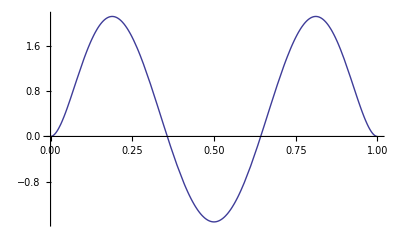

```mathematica
(* Radius error in bp *)
rError=10000*(Sqrt[x^2+y^2]-1);
Plot[rError/.{z->0.552},{t,0,1}]
```

```mathematica
dError=D[x^2+y^2,t]//FullSimplify; (* used only for solving to zero, hence omission of Sqrt[] *)
tTurn=FullSimplify[Solve[dError==0&&t≠0&&t≠1&&t≠1/2,t]⟦1⟧,z∈Reals&&z<2/3]
```

{t→(-2+3 z+√(12-z (20+3 z)))/(-4+6 z)}

```mathematica
tTurn/.{z->0.552}
```

{t→0.188641}

```mathematica
(rError/.tTurn)/.{z->0.552}
```

2.12124

```mathematica
(rError/.{t->1/2})/.{z->0.552}
```

-1.51011

```mathematica
zBest=Solve[(rError/.tTurn)==(-rError/.{t->1/2})&&z>0,z,Reals]//Flatten
```

{z→Root[2097152-23592960 #1+117129216 #1^2-342814720 #1^3+668905728 #1^4-921504768 #1^5+883891456 #1^6-515232000 #1^7+96817248 #1^8+63288000 #1^9-28977264 #1^10+466560 #1^11+18225 #1^12&,3]}

```mathematica
N[zBest,20]
```

{z→0.55191502449351057074}

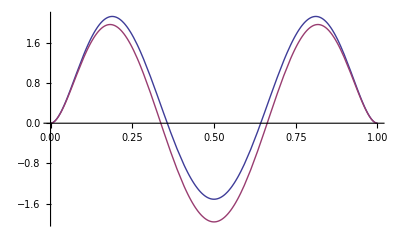

```mathematica
(* Radius error in bp *)
rError=10000*(Sqrt[x^2+y^2]-1);
Plot[{rError/.{z->0.552},rError/.zBest},{t,0,1}]
```

```mathematica
N[{   (rError/.tTurn),  (rError/.{t->1/2})   }/.zBest,20]
```

{1.9607646987687817402,-1.9607646987687817402}

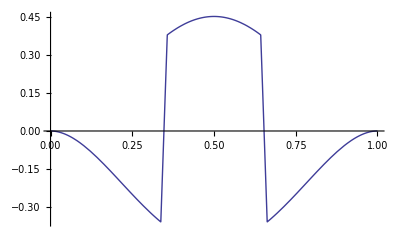

```mathematica
(* Error ’improvement’ *)
Plot[Abs[rError/.zBest]-Abs[rError/.{z->0.552}],{t,0,1}]
```

```mathematica
Print[eDiff1=((rError/.{z->0.552})-(rError/.zBest))/.{t->1/2}];
Print[eDiff2=((rError/.FindRoot[0==rError/.{z->0.552},{t,0.36}])/.zBest)];
```

0.450651

-0.378104

```mathematica
(* Change in radius, as one part in … *)
10000/eDiff1
(* If the printer is 1200 dpi then this is a one-pixel improvement if radius ≈ 47cm. *)
```

22190.1

```mathematica
(* A petal, perhaps to be painted in three pieces. *)
```

```mathematica
({{knotsX}, {knotsY}})=({{0, +4/3, +4/3, 0}, {0, +4/3, -4/3, 0}});
x=Internal`FromCoefficientList[CoeffsFromKnots[knotsX],t];
y=Internal`FromCoefficientList[CoeffsFromKnots[knotsY],t];
```

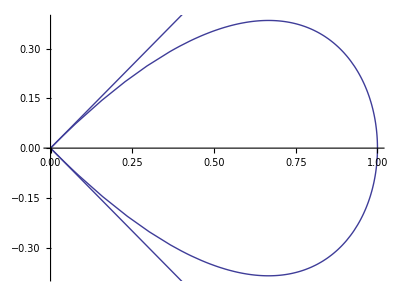

```mathematica
Show[
	ParametricPlot[{{x,y}},{t,0,1}],
	 ListLinePlot[Transpose[{knotsX,knotsY}]]
]
```

```mathematica
tMaxX=t/.Solve[D[x,t]==0&&t≥0&&t≤1/1,t]⟦1⟧//Simplify;
tMaxY=t/.Solve[D[y,t]==0&&t≥0&&t≤1/2,t]⟦1⟧//Simplify;
Print["Max X: t = ",tMaxX," ≈ ",N[tMaxX], "; {x, y} = ", ({x,y}/.{t->tMaxX})//Simplify];
Print["Max Y: t = ",tMaxY," ≈ ",N[tMaxY], "; {x, y} = ", ({x,y}/.{t->tMaxY})//Simplify," ≈ ",N[{x,y}/.{t->tMaxY}]];
```

Max X: t = 1/2 ≈ 0.5; {x, y} = {1,0}

Max Y: t = 1/6 (3-√3) ≈ 0.211325; {x, y} = {2/3,2/(3 √3)} ≈ {0.666667,0.3849}

```mathematica
Print["X upper: ",temp=SubCurveKnotsFromKnots[knotsX,0               ,tMaxY      ]//Simplify," ≈ ",N[temp]];
Print["Y upper: ",temp=SubCurveKnotsFromKnots[knotsY,0               ,tMaxY      ]//Simplify," ≈ ",N[temp]];
Print["X right: ",temp=SubCurveKnotsFromKnots[knotsX,tMaxY      ,1-tMaxY]//Simplify," ≈ ",N[temp]];
Print["Y right: ",temp=SubCurveKnotsFromKnots[knotsY,tMaxY      ,1-tMaxY]//Simplify," ≈ ",N[temp]];
Print["X lower: ",temp=SubCurveKnotsFromKnots[knotsX,1-tMaxY,1               ]//Simplify," ≈ ",N[temp]];
Print["Y lower: ",temp=SubCurveKnotsFromKnots[knotsY,1-tMaxY,1               ]//Simplify," ≈ ",N[temp]];
```

X upper: {0,-2/9 (-3+√3),-2/9 (-4+√3),2/3} ≈ {0.,0.281766,0.503989,0.666667}

Y upper: {0,-2/9 (-3+√3),2/(3 √3),2/(3 √3)} ≈ {0.,0.281766,0.3849,0.3849}

X right: {2/3,10/9,10/9,2/3} ≈ {0.666667,1.11111,1.11111,0.666667}

Y right: {2/(3 √3),2/(3 √3),-2/(3 √3),-2/(3 √3)} ≈ {0.3849,0.3849,-0.3849,-0.3849}

X lower: {2/3,-2/9 (-4+√3),-2/9 (-3+√3),0} ≈ {0.666667,0.503989,0.281766,0.}

Y lower: {-2/(3 √3),-2/(3 √3),2/9 (-3+√3),0} ≈ {-0.3849,-0.3849,-0.281766,0.}

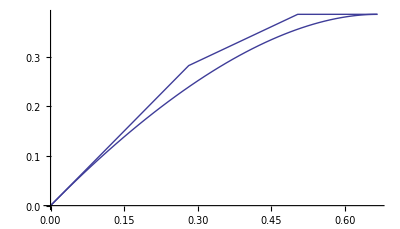

```mathematica
Show[
	ParametricPlot[{{x,y}},{t,0,tMaxY}],
	 ListLinePlot[Transpose[{SubCurveKnotsFromKnots[knotsX,0,tMaxY],SubCurveKnotsFromKnots[knotsY,0,tMaxY]}]]
]
```